```mathematica
{1,2,3,4,6}/2
```

{1/2,1,3/2,2,3}

```mathematica
rvo = RandomVariate[BinomialDistribution[10,0.5],1000]/10;
```

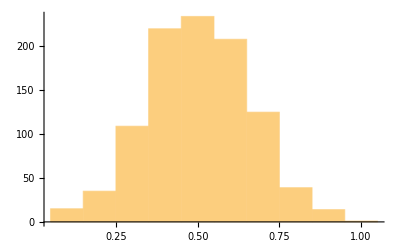

```mathematica
Histogram[rvo]
```

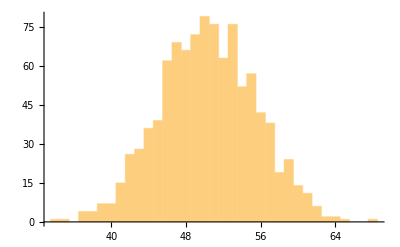

```mathematica
Histogram[RandomVariate[BinomialDistribution[100,0.5],1000]]
```

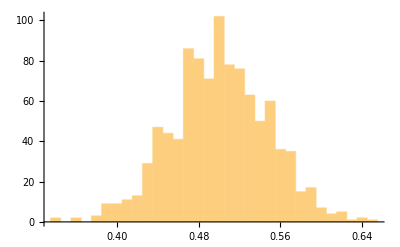

```mathematica
Histogram[RandomVariate[BinomialDistribution[100,0.5],1000]/100]
```

```mathematica
die1 = RandomVariate[DiscreteUniformDistribution[{1,6}], 10000];
```

```mathematica
die2 = RandomVariate[DiscreteUniformDistribution[{1,6}], 10000];
```

```mathematica
rvo2 = die1 + die2;
```

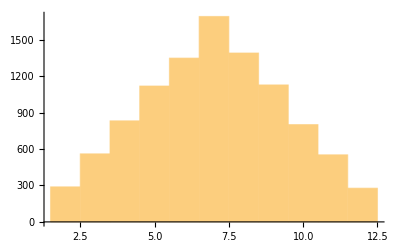

```mathematica
Histogram[rvo2]
```

```mathematica
Probability[x==2, x \[Distributed] rvo2]
```

289/10000

```mathematica
N[289/10000]
```

0.0289

```mathematica
N[Probability[x==3, x \[Distributed] rvo2]]
```

0.0561

```mathematica
N[Probability[x==5, x \[Distributed] rvo2]]
```

0.112

```mathematica
Probability[
 x + y==5, {x \[Distributed] DiscreteUniformDistribution[{1, 6}], 
  y \[Distributed] DiscreteUniformDistribution[{1,6}]}]
```

1/9

```mathematica
N[Probability[
 x + y==2, {x \[Distributed] DiscreteUniformDistribution[{1, 6}], 
  y \[Distributed] DiscreteUniformDistribution[{1,6}]}]]
```

0.0277778

```mathematica
Probability[
 x + y==5, {x \[Distributed] DiscreteUniformDistribution[{1, 6}], 
  y \[Distributed] DiscreteUniformDistribution[{1,6}]}]
```

1/9

```mathematica
Probability[
 x + y==7, {x \[Distributed] DiscreteUniformDistribution[{1, 6}], 
  y \[Distributed] DiscreteUniformDistribution[{1,6}]}]
```

1/6

```mathematica
CDF[BernoulliDistribution[0.5],0.8]
```

0.5

```mathematica
CDF[BernoulliDistribution[0.5],{0.3, 0.8}]
```

{0.5,0.5}

```mathematica
CDF[BernoulliDistribution[p]]
```

Function[x,Piecewise[{{0, x<0}, {1-p, 0≤x<1}, {1, True}}],Listable]

```mathematica
PDF[BernoulliDistribution[p]]
```

Function[x,Piecewise[{{1-p, x==0}, {p, x==1}, {0, True}}],Listable]

```mathematica
CDF[GeometricDistribution[0.5]]
```

Function[x,Piecewise[{{1-0.5^(1+Floor[x]), x≥0}, {0, True}}],Listable]

```mathematica
PDF[GeometricDistribution[p]]
```

Function[x,Piecewise[{{(1-p)^x p, x≥0}, {0, True}}],Listable]

```mathematica
Probability[
 x ==4 && y == 3, {x \[Distributed] DiscreteUniformDistribution[{1, 6}], 
  y \[Distributed] DiscreteUniformDistribution[{1,6}]}]
```

1/36

```mathematica
Probability[
 x+y ==7, {x \[Distributed] DiscreteUniformDistribution[{1, 6}], 
  y \[Distributed] DiscreteUniformDistribution[{1,6}]}]
```

1/6

```mathematica
Probability[40.2≤x≤ 59.8,x \[Distributed] BinomialDistribution[100,0.5]]
```

0.943112

```mathematica
a = TransformedDistribution[x/100, x \[Distributed] BinomialDistribution[100, 0.5]]
```

TransformedDistribution[x/100,x\[Distributed]BinomialDistribution[100,0.5]]

```mathematica
Probability[0.402≤y≤ 0.598, y \[Distributed]a]
```

0.943112